```mathematica
img=-Graphics-;
```

```mathematica
Map[MeanFilter[#, 20] &, ImagePartition[img, 10], {2}] // ImageAssemble
```

```mathematica
ImageApply[If[Abs[#-Pi/2]<0.1||Abs[#+Pi/2]<0.1,{1,1,1},#2]&,{GradientOrientationFilter[img2,4],img2}]
ImageApply[If[Abs[#-Pi/4]<0.1,{1,1,1},#2]&,{GradientOrientationFilter[img2,4],img2}]
```

```mathematica
img=-Graphics-
```

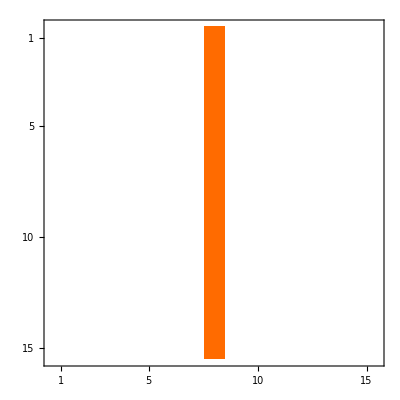
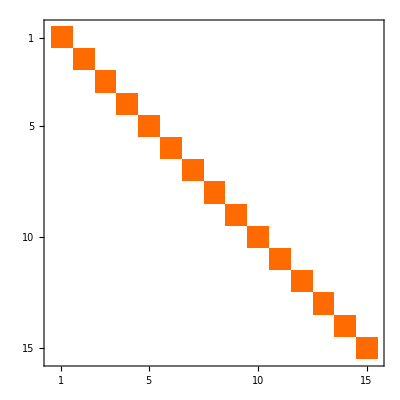
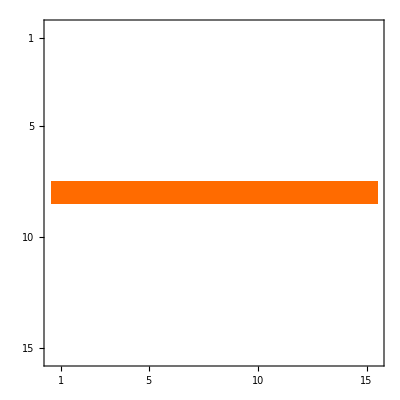
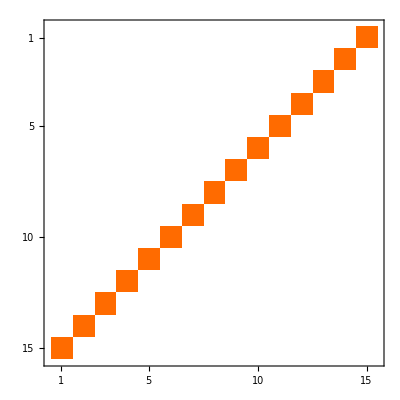

```mathematica
radius=15;
m1=ConstantArray[0,{radius,radius}];
Do[m1[[i,(1+radius)/2]]=1./radius,{i,radius}];
m2=ConstantArray[0,{radius,radius}];
Do[m2[[(1+radius)/2,i]]=1./radius,{i,radius}];
m3=ConstantArray[0,{radius,radius}];
Do[m3[[i,i]]=1./radius,{i,radius}];
m4=ConstantArray[0,{radius,radius}];
Do[m4[[i,1+radius-i]]=1./radius,{i,radius}];
kernels={m1,m3,m2,m4};
MatrixPlot/@kernels
images=ImageConvolve[img,#]&/@kernels
mask=GradientOrientationFilter[img,radius]//ClusteringComponents[#,5]&//Image//ImageAdjust
ImageApply[Switch[#,0.,#3,0.25,#4,0.5,#5,0.75,#6,1.,#3,_,#2]&,Join[{mask,img},images]]
```